# Mathematica Solutions

Andy Rothstein

arothstein@princeton.edu

Email me if you run into any errors or get stuck with something that doesn’t work!

#### 2.1

```mathematica
FullSimplify[D[(x^3 Exp[x])/(Log[x]Sin[x]),x]]
```

-(ⅇ^x x^2 Csc[x] (1-(3+x) Log[x]+x Cot[x] Log[x]))/Log[x]^2

```mathematica
x=2;
-(ⅇ^x x^2 Csc[x] (1-(3+x) Log[x]+x Cot[x] Log[x]))/Log[x]^2
```

-(4 ⅇ^2 Csc[2] (1-5 Log[2]+2 Cot[2] Log[2]))/Log[2]^2

Calling N[] gives us a decimal value

```mathematica
N[-(ⅇ^x x^2 Csc[x] (1-(3+x) Log[x]+x Cot[x] Log[x]))/Log[x]^2]
```

209.739

#### 2.2

```mathematica
A[f_]:=1/(1-(f/fpend)^2);
S[f_]:=10^-8(10/f)^2;
ASD[f_]:=A[f]^2 S[f];
```

```mathematica
fpend=1/(2π);
Solve[D[ASD[f],f]==0,f]
```

{{f→-1/(2 √3 π)},{f→1/(2 √3 π)}}

```mathematica
fpend=(√9.8)/(2π);
NSolve[D[ASD[f],f]==0,f]
```

{{f→0.287655},{f→-0.287655}}

Two things to note here: first I used NSolve[] rather than Solve since I just wanted the numerical value and this works without errors. Also, I used the := to define my functions. This means the function isn’t evaluated until it is actually called, so I can change f_pend without having the re-run the code that defines those functions.

#### 2.3

```mathematica
Integrate[x^6 Exp[-x^2]Cos[x],{x,-∞,∞}]
```

-(31 √π)/(64 ⅇ^(1/4))

#### 2.4

```mathematica
FullSimplify[Solve[(a x+x Exp[5t]+2)(x+2)==Tan[2t],x]]
```

{{x→-(1+a+ⅇ^(5 t)+√((-1+a+ⅇ^(5 t))^2+(a+ⅇ^(5 t)) Tan[2 t]))/(a+ⅇ^(5 t))},{x→-(1+a+ⅇ^(5 t)-√((-1+a+ⅇ^(5 t))^2+(a+ⅇ^(5 t)) Tan[2 t]))/(a+ⅇ^(5 t))}}

Don’t forget the spaces between a x!

#### 2.5

```mathematica
FullSimplify[Integrate[x^2 Cos[x]Exp[x],x]]
```

1/2 ⅇ^x (-1+x) ((1+x) Cos[x]+(-1+x) Sin[x])

#### 2.6

```mathematica
FullSimplify[Solve[1==A^2 Integrate[Sin[(π x)/a]^2+Sin[(2π x)/a]^2,{x,0,a}],A]]
```

{{A→-1/(√a)},{A→1/(√a)}}

#### 2.7

```mathematica
FullSimplify[2/a Integrate[Sin[(n π x)/a](1/(√a))Sin[(π x)/a]Sin[(2π x)/a],{x,0,a}],Assumptions->{n∈ Integers,a>0}]
```

-(8 (1+(-1)^n) n)/(√a (9-10 n^2+n^4) π)

#### 2.8

```mathematica
ψ[x_]=((2a)/π)^(1/4)Exp[- (a m x^2)/(1+2I ℏ a t)] √(m/(1+2 I ℏ a t));
```

```mathematica
FullSimplify[Conjugate[ψ[x]]ψ''[x],Assumptions->{{x,a,m,ℏ,t}∈ Reals}]
```

(2 √2 a ⅇ^(-(2 a m x^2)/(1+4 a^2 t^2 ℏ^2)) m (1-2 a m x^2+2 ⅈ a t ℏ) √((ⅈ m)/(ⅈ π-2 a π t ℏ)) √Abs[a] Conjugate[√(m/(1+2 ⅈ a t ℏ))])/(ⅈ-2 a t ℏ)^2

Here I removed the Abs[] and directly changed the conjugates myself.

```mathematica
Integrate[(2 √2 a ⅇ^(-(2 a m x^2)/(1+4 a^2 t^2 ℏ^2)) m (1-2 a m x^2+2 ⅈ a t ℏ) √((ⅈ m)/(ⅈ π-2 a π t ℏ)) √a √(m/(1-2 ⅈ a t ℏ)))/(ⅈ-2 a t ℏ)^2,{x,-∞,∞}]
```

ConditionalExpression[-(a^(3/2) m √(m/(1-2 ⅈ a t ℏ)) √((ⅈ m)/(ⅈ π-2 a π t ℏ)))/(√((a m)/(π+4 a^2 π t^2 ℏ^2))),Re[(a m)/(1+4 a^2 t^2 ℏ^2)]≥0]

Since our condition is satisfied, I removed the conditional expression and just simplified, although the assumptions should do that as well

```mathematica
FullSimplify[-(a^(3/2) m √(m/(1-2 ⅈ a t ℏ)) √((ⅈ m)/(ⅈ π-2 a π t ℏ)))/(√((a m)/(π+4 a^2 π t^2 ℏ^2))),Assumptions->{{a,m,ℏ,t}>0}]
```

-√a √(a m) √((ⅈ m)/(ⅈ-2 a t ℏ)) √(m+2 ⅈ a m t ℏ)

Note: sometimes Mathematica doesn’t like to combine radicals, so you may need to do it manually

```mathematica
FullSimplify[-√(a a m(ⅈ m)/(ⅈ-2 a t ℏ)(m+2 ⅈ a m t ℏ)),Assumptions->{{a,m}>0}]
```

-√(m^3) Abs[a]

#### 3.1

```mathematica
x[t_]=Exp[-t/2];
y[t_]=Log[2t];
FullSimplify[Series[x[t]/y[t],{t,1/2,2}]]
```

1/(2 ⅇ^(1/4) (t-1/2))+1/(4 ⅇ^(1/4))-(17 (t-1/2))/(48 ⅇ^(1/4))+(29 (t-1/2)^2)/(96 ⅇ^(1/4))+O[t-1/2]^3

```mathematica
Clear[y,x]
```

#### 3.2

I’ll first do it making each series it’s own function of x. There’s a slicker way to do it below using the Table[] and Range[] functions so you don’t need to do it all by hand. NOTE: You need to call Normal[] to remove the higher order error O[x]^3 term.

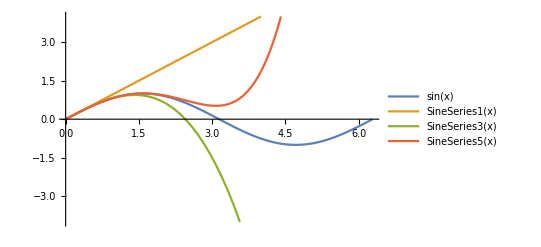

```mathematica
SineSeries1[x_]=Normal[Series[Sin[x],{x,0,1}]];
SineSeries3[x_]=Normal[Series[Sin[x],{x,0,3}]];
SineSeries5[x_]=Normal[Series[Sin[x],{x,0,5}]];
Plot[{Sin[x],SineSeries1[x],SineSeries3[x],SineSeries5[x]},{x,0,2π},PlotLegends->"Expressions",PlotRange->{{0,2π},{-4,4}}]
```

As a slicker way to do this, we make a Table[]. You can look at the info button to see how it works, but it will sweep over our Range of n’s. NOTE: We need to use Evaluate[] to make sure we get our Table of functions first, then it will try plotting those functions after. If you don’t have Evaluate[], it actually still works, but it treats the table as a single function and it will color them all the same.

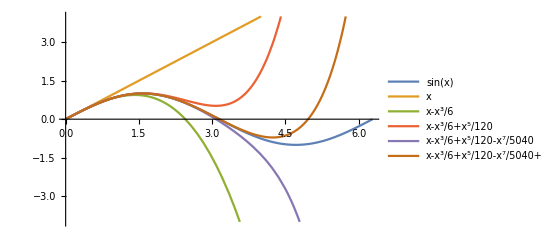

```mathematica
Plot[{Sin[x],Evaluate@Table[Normal[Series[Sin[x],{x,0,n}]],{n,Range[1,9,2]}]},{x,0,2π},PlotLegends->"Expressions",PlotRange->{{0,2π},{-4,4}}]
```

#### 4.1

```mathematica
DSolve[{t^2 y''[t]-2y[t]==3 t^2-1,y'[1]==0,y[1]==3},y[t],t]
```

{{y[t]→(4+t+t^3+2 t^3 Log[t])/(2 t)}}

Make sure you don’t forget the == and the y[t] and t

#### 4.2

```mathematica
DSolve[y'''[x]-3y''[x]+3 y'[x]-y[x]==0,y[x],x]
```

{{y[x]→ⅇ^x C[1]+ⅇ^x x C[2]+ⅇ^x x^2 C[3]}}

#### 4.3

```mathematica
DSolve[y'[x]/(1-y[x]^2)==1,y[x],x]
```

{{y[x]→(ⅇ^(2 x)-ⅇ^(2 C[1]))/(ⅇ^(2 x)+ⅇ^(2 C[1]))}}

```mathematica
y[x_,c_]=(ⅇ^(2 x)-ⅇ^(2 c))/(ⅇ^(2 x)+ⅇ^(2 c));
```

Plot in simpler way:

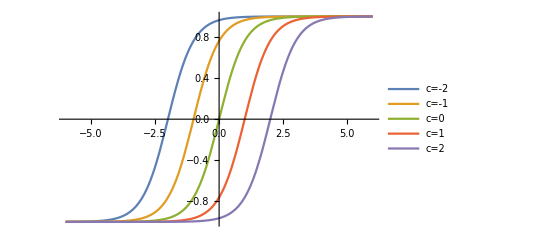

```mathematica
Plot[{y[x,-2],y[x,-1],y[x,0],y[x,1],y[x,2]},{x,-6,6},PlotLegends->{"c=-2","c=-1","c=0","c=1","c=2"}]
```

This uses a Table to go over all the values for us. Note we need to include the Evaluate function so that is creates the table first rather than plotting first.

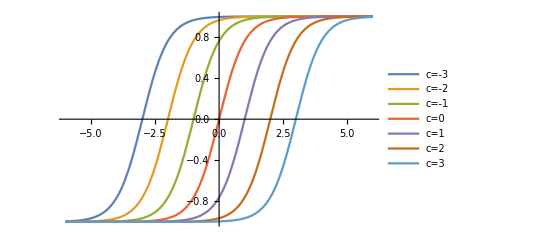

```mathematica
Plot[Evaluate@Table[y[x,c],{c,Range[-3,3]}],{x,-6,6},PlotLegends->{"c=-3","c=-2","c=-1","c=0","c=1","c=2","c=3"}]
```

#### 5.1

```mathematica
A={{2,1,0},{1,2,0},{0,0,2}};
A//MatrixForm
```

(2 | 1 | 0
1 | 2 | 0
0 | 0 | 2)

```mathematica
Eigensystem[A]//MatrixForm
```

(3 | 2 | 1
{1,1,0} | {0,0,1} | {-1,1,0})

#### 5.2

```mathematica
Eigensystem[{{Cos[θ],Exp[-I ϕ]Sin[θ]},{Exp[I ϕ]Sin[θ],-Cos[θ]}}]//MatrixForm
```

(-1 | 1
{ⅇ^(-ⅈ ϕ) (Cot[θ]-Csc[θ]),1} | {ⅇ^(-ⅈ ϕ) (Cot[θ]+Csc[θ]),1})

#### 5.3

```mathematica
A={{1,2,1},{3,-4,2},{5,1,1}};
MatrixPower[A,2].Transpose[A].Inverse[A]//MatrixForm
```

(1831/31 | 269/31 | -478/31
-371/31 | 584/31 | 9/31
1819/31 | 577/31 | -493/31)

#### 5.4

```mathematica
M={{1/4,1/3,1/3},{1/2,1/3,1/9},{1/4,1/3,5/9}};
xVec={{x},{y},{z}};
Solve[{M.xVec==xVec,x+y+z==1},{x,y,z}]
```

{{x→4/13,y→27/91,z→36/91}}

#### 5.5

```mathematica
A={{0,1,0},{0,0,1},{0,0,0}};
```

```mathematica
MatrixExp[A t]//MatrixForm
```

(1 | t | t^2/2
0 | 1 | t
0 | 0 | 1)

#### 6.1

```mathematica
r1[θ_,ϕ_]=1/2(3+Cos[2θ])Cos[2ϕ];
r2[θ_,ϕ_]=-4Cos[θ]Sin[ϕ]Cos[ϕ];
```

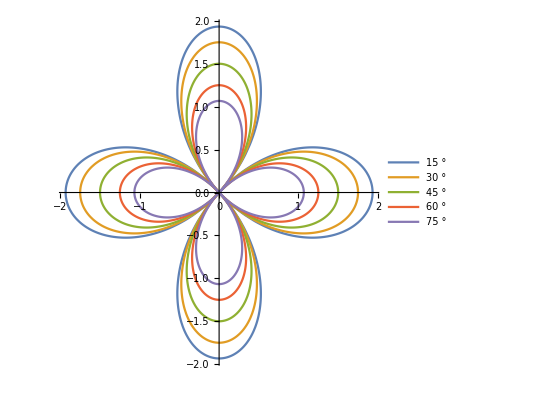

```mathematica
PolarPlot[Evaluate@Table[r1[θ,ϕ],{θ,Range[15°,75°,15°]}],{ϕ,0,2π},PlotLegends->{15°,30°,45°,60°,75°}]
```

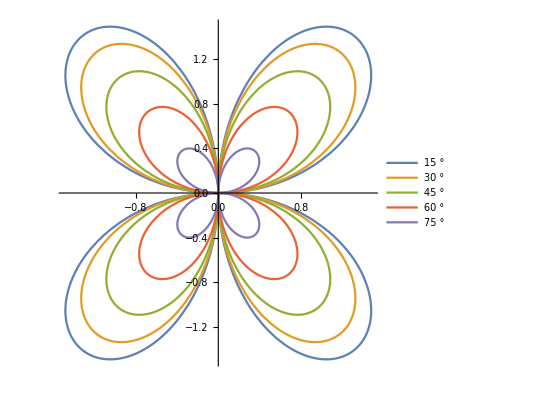

```mathematica
PolarPlot[Evaluate@Table[r2[θ,ϕ],{θ,Range[15°,75°,15°]}],{ϕ,0,2π},PlotLegends->{15°,30°,45°,60°,75°}]
```

#### 6.2

```mathematica
SphericalPlot3D[r1[θ,ϕ],{θ,0,π},{ϕ,0,2π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["Rainbow"][r]]]
```

-Graphics3D-

```mathematica
SphericalPlot3D[r2[θ,ϕ],{θ,0,π},{ϕ,0,2π},ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData["Rainbow"][r]]]
```

-Graphics3D-